ⅇ^(-k m x-1/2 k (-m+x)^2)

```mathematica
Simplify[(Sqrt[k^p/(2*Pi)^p]*Exp[-(k^p((x-m)^2/2))])/(k^(p/2-1)/((2*Pi)^(p/2)*BesselI[p/2-1,k])Exp[k x m]),Assumptions->{m^2==1,x^2==1,k>0,p>1}]
```

ⅇ^(-k m x+k^p (-1+m x)) k BesselI[-1+p/2,k]

```mathematica
ⅇ^-k k BesselI[-1+p/2,k]/
```

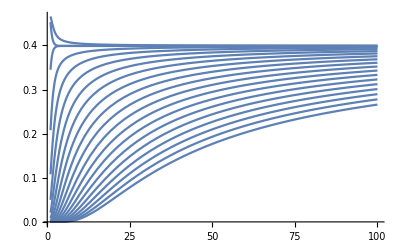

```mathematica
Plot[Table[ⅇ^-k k BesselI[-1+p/2,k]/Sqrt[k],{p,1,20}],{k,1,100}]
```

```mathematica
(Sqrt[k^p/(2*Pi)^p]*Exp[-(k ((x-m)^2/2))])/(k^(p/2-1)/((2*Pi)^(p/2)*BesselI[p/2-1,k])Exp[k x m])
```

ⅇ^(-k m x-1/2 k (-m+x)^2) k^(1-p/2) (2 π)^(p/2) √(k^p (2 π)^-p) BesselI[-1+p/2,k]

```mathematica
Simplify[((x-m)-((x-m)*m)*m)^2]
```

(-1+m^2)^2 (m-x)^2

```mathematica
{k^(p/2-1)/((2*Pi)^(p/2)*BesselI[p/2-1,k])Exp[k {Cos[t],Sin[t]} .{1,0}],2/Sqrt[(2*Pi*(1/Sqrt[k]))^p]*Exp[-((Sin[t]^2/(2/k)))]}/.{t->0,p->1}
```

{1/2 ⅇ^k Sech[k],k^(1/4) √(2/π)}

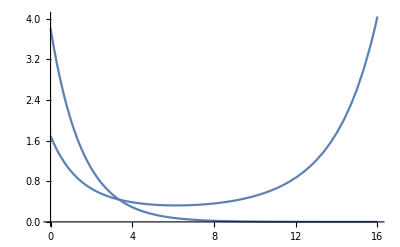

```mathematica
Plot[{{k^(p/2-1)/((2*Pi)^(p/2)*BesselI[p/2-1,k])Exp[k {Cos[t],Sin[t]} .{1,0}],2/Sqrt[(2*Pi*(1/Sqrt[k]))^(p-1)]*Exp[-((Sin[t]^2/(2/k)))]}/.{t->0,k->3}},{p,0,16}]
```

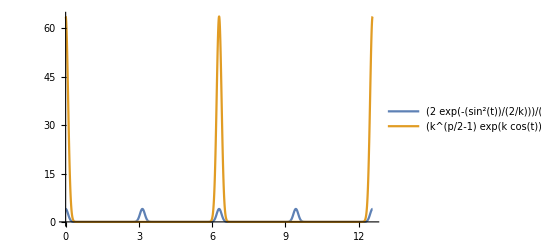

```mathematica
Plot[{2/Sqrt[(2*Pi*(1/Sqrt[k]))^p]*Exp[-((Sin[t]^2/(2/k)))]/.{k->100,p->3},k^(p/2-1)/((2*Pi)^(p/2)*BesselI[p/2-1,k])Exp[k *Cos[t]]/.{k->100,p->4}},{t,0,4 π},PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
Sqrt[k^p/(2*Pi)^p]*Exp[-(k (({Cos[t],Sin[t]} -{1,0}).({Cos[t],Sin[t]} -{1,0})/2))])/.{k->10,p->2}
```

```mathematica
Plot[Sqrt[k^p/(2*Pi)^p]*Exp[-(k (({Cos[t],Sin[t]} -{1,0}).({Cos[t],Sin[t]} -{1,0})/2))])/.{k->10,p->2},{t,0,3 π}]
```

```mathematica
Sqrt[k^p/(2*Pi)^p]*Exp[-(k (({Cos[t],Sin[t]} -{1,0}).({Cos[t],Sin[t]} -{1,0})/2))]/.{k->10,p->2}
```

(5 ⅇ^(-5 ((-1+Cos[t])^2+Sin[t]^2)))/π

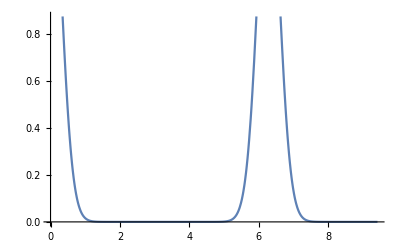

```mathematica
Plot[(5 ⅇ^(-5 ((-1+Cos[t])^2+Sin[t]^2)))/π,{t,0,3 π}]
```

```mathematica
Nor
```

```mathematica
vMF[t_,k_,p_]:=k^(p/2-1)/((2*Pi)^(p/2)*BesselI[p/2-1,k])*Exp[k *Cos[t]]
```

```mathematica
Integrate[vMF[t,10,2],{t,0,2*Pi}]
```

1

2.57761

```mathematica
vMF[t,k,p]
```

(ⅇ^(k Cos[t]) k^(-1+p/2) (2 π)^(-p/2))/BesselI[-1+p/2,k]

```mathematica
pNorm[t_,s_,p_]:=1/Sqrt[(2*Pi*s^2)^p]*Exp[-(((Sin[t]/s)^2)/2)]
```

```mathematica
pNorm[t,s,p]
```

(ⅇ^(-Sin[t]^2/(2 s^2)))/(√((2 π)^p (s^2)^p))

```mathematica
Manipulate[Plot[{pNorm[t,s,p],vMF[t,1/s^2,p+1]},{t,-2.1689772148491038,2.1689772148491038},PlotRange->All],{p,1,100},{s,0.0001,1}]
```

```mathematica
N[Integrate[pNorm[t,0.1,1]/vMF[t,100,1],{t,-Pi/2,Pi/2}]]
```

4.17991×10^20

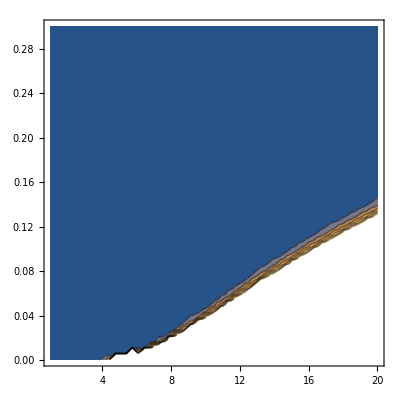

```mathematica
ContourPlot[(ⅇ^(-1/(4 s^2)) π BesselI[0,1/(4 s^2)])/(√((2 π)^p (s^2)^p)),{p,1,20},{s,0.001,0.3}]
```

```mathematica
N[BesselI[0,1/400]/(20 ⅇ^(1/400))]
```

0.0498752

```mathematica
N[(√(π/2) BesselI[0,1/4])/ⅇ^(1/4)]
```

0.991393

```mathematica
N[((5/2)^(1/4) √π BesselI[0,5/2])/ⅇ^(5/2)]
```

0.601864

```mathematica
N[(2^(1/4) 5^(3/4) √π BesselI[0,250])/ⅇ^250]
```

0.177917

```mathematica
Plot[Table[{pNorm[t,.2,p-1]/vMF[t,(1/.2)^2,p]},{p,2,100}],{t,-Pi/5,Pi/5},PlotRange->All]
```

$Aborted

```mathematica
Manipulate[Plot[Log[(pNorm[0,s,p-1]/vMF[0,(1/s)^2,p])],{p,2,1000},PlotRange->All],{s,0.001,1}]
```